```mathematica
bm
```

{{5000,-0.118762,0.0331378,-0.13479},{10000,-0.075061,-0.0270807,-0.0748406},{15000,-0.055518,-0.0602772,-0.0737713},{20000,-0.0283997,-0.114657,-0.0559004},{25000,-0.0324355,-0.0381275,-0.118853},{30000,-0.0213915,-0.150919,-0.0253666},{35000,-0.0967732,-0.043907,-0.0668113},{40000,-0.0654176,-0.0893762,-0.0557254},{45000,-0.0510545,-0.135379,-0.0206207},{50000,-0.0301765,-0.138342,-0.0387071},{55000,-0.0376717,-0.130429,-0.045918},{60000,-0.0539009,-0.0846641,-0.0730374},{65000,-0.0687941,-0.111509,-0.037082},{70000,-0.0408831,-0.109994,-0.0535979},{75000,-0.035799,-0.165939,-0.0116053},{80000,-0.0508014,-0.0780531,-0.0805913},{85000,-0.0641763,-0.125563,-0.0226021},{90000,-0.0311391,-0.149623,-0.0332883},{95000,0.0355245,-0.126147,-0.118679},{100000,-0.0761867,-0.0826207,-0.0537563},{105000,-0.0220158,-0.134673,-0.0559293},{110000,-0.0224537,-0.090018,-0.0970541},{115000,-0.0236667,-0.113355,-0.0751461},{120000,-0.01464,-0.0851137,-0.114643},{125000,-0.0555101,-0.134417,-0.0229665},{130000,-0.011287,-0.110429,-0.090293},{135000,-0.0181233,-0.12443,-0.0668125},{140000,0.0219258,-0.109995,-0.116426},{145000,-0.00793353,-0.120184,-0.081641},{150000,0.00682172,-0.151882,-0.0633751},{155000,-0.0309112,-0.079806,-0.101798},{160000,-0.0490996,-0.107268,-0.0565097},{165000,-0.0103355,-0.106532,-0.0943048},{170000,-0.0405353,-0.116162,-0.0490445},{175000,-0.0555021,-0.11155,-0.039996},{180000,-0.0167947,-0.108716,-0.0801391},{185000,-0.039005,-0.113602,-0.0551533},{190000,-0.047527,-0.103465,-0.0562554},{195000,-0.0743176,-0.0114278,-0.131828}}

```mathematica
(*test of nMeas w/ ne=4, 0.05*0.05 loop, steplength = 0.01.*)
```

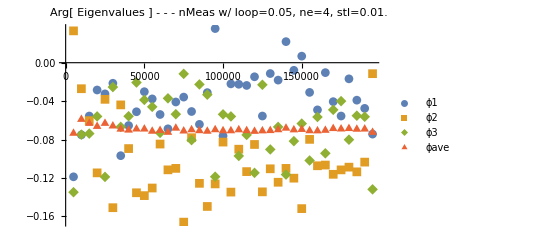

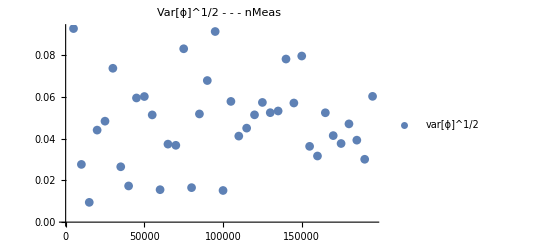

```mathematica
bm=Import["Google Drive/jie_programs/QHlattice/test_error/test_error_stl_sl_4_new","Table"];
n:=Length[bm]
x=Table[bm[[i]][[1]],{i,1,n}];
phase1= Table[{x[[i]],bm[[i]][[2]]},{i,1,n}];
phase2= Table[{x[[i]],bm[[i]][[3]]},{i,1,n}];
phase3= Table[{x[[i]],bm[[i]][[4]]},{i,1,n}];
ave=Table[(bm[[i]][[2]]+bm[[i]][[3]]+bm[[i]][[4]])/3,{i,n}];
phaseave= Table[{x[[i]],ave[[i]]},{i,1,n}];
ϕ1dif= Table[{x[[i]],bm[[i]][[2]]-ave[[i]]},{i,1,n}];
ϕ2dif= Table[{x[[i]],bm[[i]][[3]]-ave[[i]]},{i,1,n}];
ϕ3dif= Table[{x[[i]],bm[[i]][[4]]-ave[[i]]},{i,1,n}];


ListPlot[{phase1,phase2,phase3,phaseave},PlotLegends->{"ϕ1","ϕ2", "ϕ3","ϕave"},PlotMarkers->Automatic, PlotLabel->"Arg[ Eigenvalues ] - - - nMeas w/ loop=0.05, ne=4, stl=0.01."(*,PlotRange->{{0,200000},{-0.2,0.0}}*)]

phase=Table[Table[bm[[k]][[i]],{k,n}],{i,2,4}];
varphase=Table[{x[[i]],Variance[phase][[i]]},{i,n}];
svarphase=Table[{x[[i]],√(Variance[phase][[i]])},{i,n}];
varphase2=Table[{x[[i]],Variance[phase][[i]]/(ave[[i]])^2},{i,n}];
ListPlot[svarphase,PlotLegends->{"var[ϕ]^1/2"},PlotMarkers->Automatic, PlotLabel->"Var[ϕ]^1/2 - - - nMeas"]
```